## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/mercury/snake/";  
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/mercury/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 1.97091 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Apr 22, 2020, time: 16:55:39

nb: /Users/dantopa/Mathematica_files/nb/ert/mercury/snake/rescale-01.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 1.97091 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
ipad=ImagePadding->{{Automatic,3},{Automatic,Automatic}};
```

```mathematica
isize=ImageSize->5 72;
```

#### functions

#### substitutions

#### modules

## 2

### import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
σ=meanRCS[[1]];
{M,𝒩}=Dimensions[meanRCS]
```

{28,361}

```mathematica
S=meanRCSᵀ;
```

```mathematica
mx=Max[meanRCS]
mn=Min[meanRCS]
```

59.2522

0.798997

## sequence

```mathematica
k=90;
ListPlot[{Range[3,30],S[[k]]}ᵀ,
PlotRange->{{2,31},{-1,62}},
PlotStyle->Blue,
PlotLabel->"Yaw angle α = "<>ToString[-180+k-1],
Frame->True,
FrameLabel->{"Radar Frequency, MHz","Mean Total Cross Section, sq m"},
ipad]
```

```mathematica
Dimensions[Sᵀ]
```

```mathematica
k=91;
b=S[[k]]
```

{42.9174,30.0549,27.2826,27.5963,31.6633,36.4519,39.363,38.4163,41.4149,44.7781,48.8126,53.6002,57.4762,59.2522,57.7514,54.0373,50.3697,48.4284,48.5161,49.6048,49.9665,49.9648,50.8409,52.6271,53.3859,53.7889,53.6134,55.992}

```mathematica
gpts=ListPlot[{Range[3,30],b}ᵀ,
PlotRange->{{2,31},{-1,62}},
PlotStyle->Purple,
PlotLabel->"Yaw angle α = "<>ToString[-180+k-1],
Frame->True,
FrameLabel->{"Radar Frequency, MHz","Mean Total Cross Section, sq m"},
ipad]
```

## frequency

```mathematica
ν=Range[3,30]
```

{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
μ=(2/27 #-11/9)&/@ν;
%//N
```

{-1.,-0.925926,-0.851852,-0.777778,-0.703704,-0.62963,-0.555556,-0.481481,-0.407407,-0.333333,-0.259259,-0.185185,-0.111111,-0.037037,0.037037,0.111111,0.185185,0.259259,0.333333,0.407407,0.481481,0.555556,0.62963,0.703704,0.777778,0.851852,0.925926,1.}

## fit

### pose problem

```mathematica
d=7;
basis=Table[𝓍^k,{k,0,d}];
𝒩=d+1;
m=Length[μ]
```

28

### linear system

```mathematica
one=Table[1,{m}];
A={one};
vector=1;
Do[
vector=vector μ;
AppendTo[A,vector]
,{k,d}];
A=Aᵀ;
```

```mathematica
A//mf//N
```

(1. | -1. | 1. | -1. | 1. | -1. | 1. | -1.
1. | -0.925926 | 0.857339 | -0.793832 | 0.73503 | -0.680583 | 0.63017 | -0.58349
1. | -0.851852 | 0.725652 | -0.618148 | 0.52657 | -0.44856 | 0.382107 | -0.325498
1. | -0.777778 | 0.604938 | -0.470508 | 0.36595 | -0.284628 | 0.221377 | -0.172182
1. | -0.703704 | 0.495199 | -0.348473 | 0.245222 | -0.172564 | 0.121434 | -0.0854533
1. | -0.62963 | 0.396433 | -0.249606 | 0.157159 | -0.0989523 | 0.0623033 | -0.039228
1. | -0.555556 | 0.308642 | -0.171468 | 0.0952599 | -0.0529221 | 0.0294012 | -0.016334
1. | -0.481481 | 0.231824 | -0.111619 | 0.0537426 | -0.025876 | 0.0124588 | -0.0059987
1. | -0.407407 | 0.165981 | -0.0676218 | 0.0275496 | -0.0112239 | 0.00457271 | -0.00186296
1. | -0.333333 | 0.111111 | -0.037037 | 0.0123457 | -0.00411523 | 0.00137174 | -0.000457247
1. | -0.259259 | 0.0672154 | -0.0174262 | 0.00451791 | -0.00117131 | 0.000303673 | -0.0000787299
1. | -0.185185 | 0.0342936 | -0.00635066 | 0.00117605 | -0.000217787 | 0.0000403309 | -7.46868×10^-6
1. | -0.111111 | 0.0123457 | -0.00137174 | 0.000152416 | -0.0000169351 | 1.88168×10^-6 | -2.09075×10^-7
1. | -0.037037 | 0.00137174 | -0.0000508053 | 1.88168×10^-6 | -6.96917×10^-8 | 2.58117×10^-9 | -9.55991×10^-11
1. | 0.037037 | 0.00137174 | 0.0000508053 | 1.88168×10^-6 | 6.96917×10^-8 | 2.58117×10^-9 | 9.55991×10^-11
1. | 0.111111 | 0.0123457 | 0.00137174 | 0.000152416 | 0.0000169351 | 1.88168×10^-6 | 2.09075×10^-7
1. | 0.185185 | 0.0342936 | 0.00635066 | 0.00117605 | 0.000217787 | 0.0000403309 | 7.46868×10^-6
1. | 0.259259 | 0.0672154 | 0.0174262 | 0.00451791 | 0.00117131 | 0.000303673 | 0.0000787299
1. | 0.333333 | 0.111111 | 0.037037 | 0.0123457 | 0.00411523 | 0.00137174 | 0.000457247
1. | 0.407407 | 0.165981 | 0.0676218 | 0.0275496 | 0.0112239 | 0.00457271 | 0.00186296
1. | 0.481481 | 0.231824 | 0.111619 | 0.0537426 | 0.025876 | 0.0124588 | 0.0059987
1. | 0.555556 | 0.308642 | 0.171468 | 0.0952599 | 0.0529221 | 0.0294012 | 0.016334
1. | 0.62963 | 0.396433 | 0.249606 | 0.157159 | 0.0989523 | 0.0623033 | 0.039228
1. | 0.703704 | 0.495199 | 0.348473 | 0.245222 | 0.172564 | 0.121434 | 0.0854533
1. | 0.777778 | 0.604938 | 0.470508 | 0.36595 | 0.284628 | 0.221377 | 0.172182
1. | 0.851852 | 0.725652 | 0.618148 | 0.52657 | 0.44856 | 0.382107 | 0.325498
1. | 0.925926 | 0.857339 | 0.793832 | 0.73503 | 0.680583 | 0.63017 | 0.58349
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

### solution

```mathematica
W=A†.A;
c=Inverse[W].A†.b
```

{54.9605,-2.33823,-57.6739,55.9062,64.3613,-34.7963,-13.7603,-12.029}

```mathematica
g[𝓍_]=c.basis
```

54.9605-2.33823 𝓍-57.6739 𝓍^2+55.9062 𝓍^3+64.3613 𝓍^4-34.7963 𝓍^5-13.7603 𝓍^6-12.029 𝓍^7

```mathematica
r=A.c-b;
𝓈=√((r.r)/(m-𝒩)Diagonal[Inverse[W]])
```

{1.09415,5.57353,12.5492,38.3273,32.4596,75.6329,22.0744,43.8559}

```mathematica
Abs[c]/𝓈
```

{50.2311,0.419524,4.59583,1.45865,1.98281,0.460068,0.623359,0.274284}

### plot

```mathematica
gpts=ListPlot[{μ,b}ᵀ,
PlotRange->{Automatic,{-1,62}},
PlotStyle->Purple,
PlotLabel->"Yaw angle α = "<>ToString[-180+k-1],
Frame->True,
FrameLabel->{"Radar Frequency, MHz","Mean Total Cross Section, sq m"},
ipad]
```

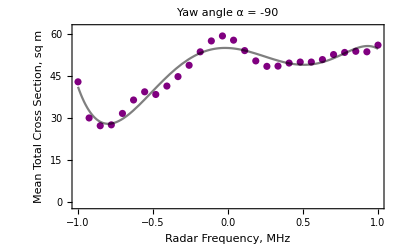

```mathematica
gplot=Plot[g[x],{x,-1,1},PlotStyle->{Black,Opacity[0.5]}];Show[{gpts,gplot}]
```

## loop

### pose problem

```mathematica
d=7;
basis=Table[𝓍^k,{k,0,d}];
𝒩=d+1;
m=Length[μ]
```

28

### prep

```mathematica
ν=Range[3,30];
```

```mathematica
μ=(2/27 #-11/9)&/@ν;
%//N
```

{-1.,-0.925926,-0.851852,-0.777778,-0.703704,-0.62963,-0.555556,-0.481481,-0.407407,-0.333333,-0.259259,-0.185185,-0.111111,-0.037037,0.037037,0.111111,0.185185,0.259259,0.333333,0.407407,0.481481,0.555556,0.62963,0.703704,0.777778,0.851852,0.925926,1.}

```mathematica
one=Table[1,{m}];
A={one};
vector=1;
Do[
vector=vector μ;
AppendTo[A,vector]
,{k,d}];
A=Aᵀ;
W=A†.A;
Winv=Inverse[W];
det=Det[W]//N
```

0.000369424

```mathematica
s=SingularValueList[A];
κ=First[s]/Last[s]//N
```

214.949

```mathematica
Det[W]//N
```

0.000369424

### loop

```mathematica
file=dirData<>"monomial-d-"<>pad[d]<>".txt";
rslt=OpenWrite[file,PageWidth->Infinity];
(* tag source file *)
mark;
Write[rslt,dirHome,nb];
Write[rslt,time," ",date];
Write[rslt,""];
(* mesh *)
Write[rslt,"degree of fit: ",d];
Write[rslt,"mesh:"];
Write[rslt,μ];
Write[rslt,μ//N];
Write[rslt,"dimensions A = ",Dimensions[A]];
Write[rslt,"kappa(A) = ",κ];
Write[rslt,"det W: ",det];
Write[rslt,"Diagonal[Winv]: ",Diagonal[Winv]//N];
Write[rslt,""];
(* init *)
mxerr=-∞;
mnerr=∞;
smerr=0;
cnterr=0;
myerr={};
(* loop *)
Do[
b=S[[k]];
Write[rslt,""];
α=k-180-1;
Write[rslt,"k = ",k,"; alpha = ",α];
Write[rslt,"data vector:"];
Write[rslt,b];
(* solution *)
c=LeastSquares[A,b];
r=A.c-b;
te=r.r;
smerr=smerr+te;
cnterr++;
If[te>mxerr,mxerr=te;kmax=k;];
If[te<mnerr,mnerr=te;kmin=k];
myerr=AppendTo[myerr,{α,te}];
g[𝓍_]=c.basis;
𝓈=√((r.r)/(m-𝒩)Diagonal[Winv]);
sn=Abs[c]/𝓈;
counter=0;
(If[#<1,counter++])&/@sn;
(* output *)
Write[rslt,"Mean = ",FortranForm[Mean[b]]];
Write[rslt,"solution vector:"];
Write[rslt,c];
Write[rslt,"solution errors:"];
Write[rslt,𝓈];
Write[rslt,"solution function:"];
Write[rslt,g[x]];
Write[rslt,"residual error vector:"];
Write[rslt,r];
Write[rslt,"Sum of residuals = ",FortranForm[Total[r]]];
Write[rslt,"Standard deviation of residuals = ",FortranForm[StandardDeviation[r]]];
Write[rslt,"r^2 = ",te];
Write[rslt,"amplitude signal-to-noise:"];
Write[rslt,sn];
Write[rslt,"number where signal/noise < 1: ",counter, " of ",d+1," (",Round[1000 counter/(d+1)]/10//N,"%)"];
Write[rslt,"Mean value of data vector = ",Mean[b]];
,{k,360}];
Write[rslt,""];
Write[rslt,"Mean error = ",smerr/cnterr];
Write[rslt,"Maximum total error of ",mxerr," at k = ",kmax," (",kmax-181," deg)"];
Write[rslt,"Minimum total error of ",mnerr," at k = ",kmin," (",kmin-181," deg)"];
Write[rslt,""];
Write[rslt,""];
Close[rslt];
edit[file]
```

Removing quotes from /Users/dantopa/Mathematica_files/io/ert/mercury/snake/data/monomial-d-07.txt

```mathematica
file=dirData<>"error-log-"<>pad[d]<>".txt";
rslt=OpenWrite[file,PageWidth->Infinity];
(* tag source file *)
mark;
Write[rslt,dirHome,nb];
Write[rslt,time," ",date];
Write[rslt,""];
(* mesh *)
Write[rslt,"Spectrum of total error:"];
Write[rslt,myerr];
Close[rslt];
edit[file]
```

Removing quotes from /Users/dantopa/Mathematica_files/io/ert/mercury/snake/data/error-log-07.txt

## summary

```mathematica
gworst=ListPlot[{myerr[[181]]},PlotStyle->{Red,PointSize[0.02]}];
gbest=ListPlot[{myerr[[282]]},PlotStyle->{Green,PointSize[0.02]}];
```

```mathematica
g101=ListPlot[myerr,
ipad,
isize,
Frame->True,
FrameLabel->{"Yaw angle, °","Total Squared Error"},
PlotStyle->Black,
PlotLabel->"Sciacca Airframe"<>lf<>"Total Squared Error vs. Yaw Angle"];
```

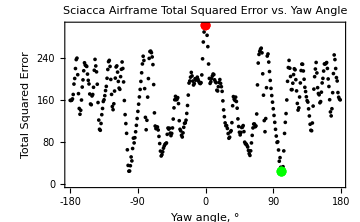

```mathematica
g102=Show[{g101,gbest,gworst},
ipad,
FrameTicks->{{Automatic,Automatic},{Range[-180,180,45],Automatic}}]
```

```mathematica
Export[dirData<>"scatter-error.pdf",g102]
```

/Users/dantopa/Mathematica_files/io/ert/mercury/snake/data/scatter-error.pdf

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```